```mathematica
files = FileNames["2efuncs.tab"];
datas = Drop[Import[#], 1]&/@files;
ch1s=Transpose[{#[[All,1]],#[[All,2]]}]&/@datas;
ch2s=Transpose[{#[[All,1]],#[[All,3]]}]&/@datas;
data = Transpose[{ch1s, ch2s}];
fitdata = Table[Select[data[[i, 2]], #[[1]]≥ 0.0054 && #[[1]]≤0.013&], {i, 1, Length[data]}];
nlms = NonlinearModelFit[#, a - b ⅇ^(-c x), {a, b, c}, x]&/@fitdata;
funcs = Normal[#]&/@ nlms;
```

NonlinearModelFit::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

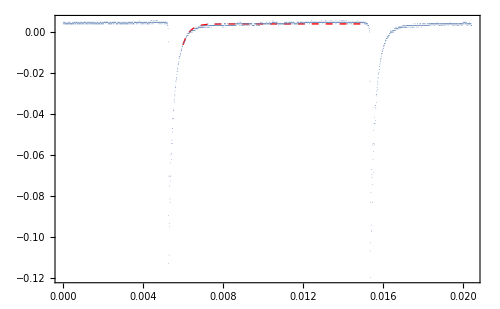

```mathematica
Show[Plot[#[[2]], {x, 0.006, 0.015},ImageSize->500, PlotRange->All, Frame->True, PlotStyle->{Red, Dashed, Thick}], ListPlot[#[[1, 2]],PlotStyle->{PointSize[0.00001]}]]&/@ Transpose[{data, funcs}]
```

{866.835,511.784,424.835,438.611,392.718,341.533}

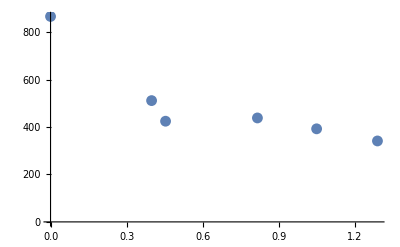

```mathematica
taus=#["ParameterTableEntries"][[3, 1]]&/@ nlms
filters = Drop[{0.,0.398736,0.453891,0.816374,1.04996,1.29003,1.49831,1.65801}, -2];
ListPlot[Transpose[{filters, taus}], PlotRange->All]
```

```mathematica
taudata = Transpose[{1/10^Drop[filters, 0], Drop[taus, 0]}]
```

{{1.,866.835},{0.399268,511.784},{0.351649,424.835},{0.152625,438.611},{0.0891333,392.718},{0.0512826,341.533}}

```mathematica
taufit = NonlinearModelFit[taudata, a + b x, {a, b}, x]
```

FittedModel[317.054+525.448 x]

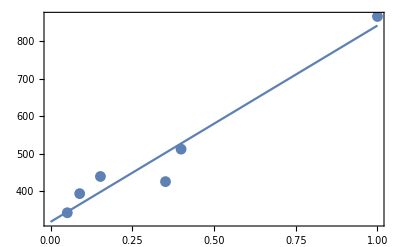

```mathematica
Show[Plot[Normal[taufit], {x, 0, 1}, Frame->True, PlotRange->All], ListPlot[taudata]]
```

```mathematica
1/317.0535636489682
```

0.00315404